```mathematica
skewedVoigt[μ_,δ_,σ_,skew_,x_]:=PDF[VoigtDistribution[δ,σ],(x-μ)]*(1+Erf[(skew(x-μ))/(σ √2)])
smooth[lis_,w_]:=(t=1/(∑_(i=-w)^w 1/(Abs[i]+1))Table[1/(Abs[i]+1)*lis[[1+w+i;;-1-(w-i)]],{i,-w,w}];
smoothedLis=∑_(i=1)^(2*w+1) t[[i]])
findXMax[dSet_]:=(xdat=dSet[[All,1]];
ydat=dSet[[All,2]];
posit=Position[ydat,Max[ydat]][[1,1]];
xdat[[posit]])

(*sampleLocalMax[hList_,nSamp_,res_,smoothWidth_]:=(
rSamp=RandomSample[hList,nSamp];
{xSample,ySample}=HistogramList[rSamp,{res}];
smoothY=smooth[ySample,smoothWidth];
smoothX=smooth[(xSample[[2;;]]+xSample[[;;-2]])/2,smoothWidth];
smoothData=Transpose[{smoothX,smoothY}];
{findXMax[smoothData],smoothData})*)
sampleLocalMax[wList_,fList_,nSamp_,res_,smoothWidth_]:=(
rSamp=RandomChoice[wList->fList,nSamp];
{xSample,ySample}=HistogramList[rSamp,{res}];
smoothY=smooth[ySample,smoothWidth];
smoothX=smooth[(xSample[[2;;]]+xSample[[;;-2]])/2,smoothWidth];
smoothData=Transpose[{smoothX,smoothY}];
{findXMax[smoothData],smoothData})

sampleLocalMax2[wList_,fList_,nSamp_,res_,smoothWidths_]:=(
rSamp=RandomChoice[wList->fList,nSamp];
{xSample,ySample}=HistogramList[rSamp,{res}];
smoothDatasets=Table[(
smoothY=smooth[ySample,smoothWidth];
smoothX=smooth[(xSample[[2;;]]+xSample[[;;-2]])/2,smoothWidth];
smoothData=Transpose[{smoothX,smoothY}];
{findXMax[smoothData],smoothData}),{smoothWidth,smoothWidths}])

SubSampleDistMaker[wList_,fList_,nPoints_,res_,smoothingW_,n_]:=Table[sampleLocalMax[wList,fList,nPoints,res,smoothingW][[1]],{i,1,n}]
SubSampleDistMaker2[wList_,fList_,nPoints_,res_,smoothingWs_,n_]:=Table[sampleLocalMax2[wList,fList,nPoints,res,smoothingWs][[All,1]],{i,1,n}]

(*intFunc[func_,k1_,k2_]:=NIntegrate[N[func[x]],{x,k1,k2}]
intFunc[f,13280,13280.1]
6.012278942190535*)
(*interpF=ListInterpolation[weights,freqs]
integrolate[f_]:=Integrate[interpF[x],{x,f-.005,f+.005}]
integrolate[13281]*)
findPolyMax[dset_,p_,{guessLBound_,guessRBound_}]:=(
g=(guessLBound+guessRBound)/2;
pollys=Table[(x-g)^n,{n,0,p}];
fitFunc=Fit[dset,pollys,x];
nmaxFit=NMaximize[{fitFunc/.(x-g)->x,guessLBound-g≤x≤guessRBound-g},x][[2]];
xMaxFitFunc=(x/.nmaxFit)+g
(*{xMaxFitFunc}*)
)
sampleLocalMax3[wList_,fList_,nPoints_,{f1_,f2_,resolution_},smoothWidths_,p_,{guessLBound_,guessRBound_}]:=(
rSamp=RandomChoice[wList->fList,nPoints];
{xSample,ySample}=HistogramList[rSamp,{Table[f,{f,f1,f2,resolution}]}];
smoothDatasets=Table[(
smoothY=smooth[ySample,smoothWidth];
smoothX=smooth[(xSample[[2;;]]+xSample[[;;-2]])/2,smoothWidth];
smoothData=Transpose[{smoothX,smoothY}];
{findPolyMax[smoothData,p,{guessLBound,guessRBound}],smoothData}),{smoothWidth,smoothWidths}])

SubSampleDistMaker3[wList_,fList_,nPoints_,{f1_,f2_,step_},smoothWidths_,p_,{guessLBound_,guessRBound_},n_]:=Table[sampleLocalMax3[wList,fList,nPoints,{f1,f2,step},smoothWidths,p,{guessLBound,guessRBound}][[All,1]],{i,1,n}]
(*l=1;m={1};
{Length[l],Length[{l}]}
{Length[Flatten[{l}]],Length[Flatten[{m}]]}
{0,1}
{1,1}*)
sampleLocalMax4[wList_,fList_,nPoints_,{f1_,f2_,resolution_},smoothWidth_,p_,{guessLBound_,guessRBound_}]:=(
Assert[smoothWidth∈Integers];
rSamp=RandomChoice[wList->fList,nPoints];
{xSample,ySample}=HistogramList[rSamp,{Table[f,{f,f1,f2,resolution}]}];
smoothY=smooth[ySample,smoothWidth];
smoothX=smooth[(xSample[[2;;]]+xSample[[;;-2]])/2,smoothWidth];
smoothData=Transpose[{smoothX,smoothY}];
{findPolyMax[smoothData,p,{guessLBound,guessRBound}],smoothData})

SubSampleDistMaker4[wList_,fList_,nPoints_,{f1_,f2_,step_},smoothWidth_,p_,{guessLBound_,guessRBound_},n_]:=(
If[Length[Flatten[{smoothWidth}]]==1,Table[sampleLocalMax4[wList,fList,nPoints,{f1,f2,step},Flatten[{smoothWidth}][[1]],p,{guessLBound,guessRBound}][[1]],{i,1,n}],
Table[sampleLocalMax3[wList,fList,nPoints,{f1,f2,step},smoothWidth,p,{guessLBound,guessRBound}][[All,1]],{i,1,n}]])
```

```mathematica
massCounts=<|242-> 2325177,243-> 771584,244->413663,245-> 2529577,247-> 604009|>;
```

```mathematica
parms242=<|const->314.853,
μ0->13285.0034,Γ0->1.852,σ0->0.559,skew0->-3.549, amp0->3128.6935,
μ1->13278.8381,Γ1->1.734,σ1->0.167,skew1->-1.,amp1->1618.448,
μ2->13272.7352,Γ2->1.7058,σ2->0.144,skew2->-1.005,amp2->717.439,
μ3->13266.7536,Γ3->1.9194,σ3->0.110,skew3->-1.,amp3->229.483|>;
```

```mathematica
parms243=<|const->93.087,
μ0->13284.9089,Γ0->2.03,σ0->0.220,skew0->-1.256, amp0->825.67,
μ1->13278.7584,Γ1->1.415,σ1->0.935,skew1->-4.,amp1->410.736,
μ2->13272.6378,Γ2->1.823,σ2->0.701,skew2->-3.979,amp2->195.270,
μ3->13266.5648,Γ3->2.815,σ3->0.252,skew3->-2.11,amp3->91.602|>;
```

```mathematica
parms244=<|const->47.698,
μ0->13284.8420,Γ0->2.114,σ0->0.350,skew0->-1.513, amp0->276.617,
μ1->13278.5858,Γ1->1.903,σ1->0.160,skew1->-1.002,amp1->124.370,
μ2->13272.5761,Γ2->1.854,σ2->0.354,skew2->-1.039,amp2->63.636,
μ3->3266.4303,Γ3->1.854,σ3->0.772,skew3->-3.664,amp3->41.432|>;
```

```mathematica
parms245=<|const->326.845,
μ0->13284.7393,Γ0->1.869,σ0->0.479,skew0->-3.539, amp0->3173.979,
μ1->13278.5695,Γ1->1.593,σ1->0.298,skew1->-2.251,amp1->1547.113,
μ2->13272.4646,Γ2->1.844,σ2->0.461,skew2->-3.397,amp2->724.971,
μ3->13266.4420,Γ3->1.760,σ3->0.100,skew3->-1.190,amp3->206.140|>;
```

```mathematica
parms247=<|const->63.312,
μ0->13284.5336,Γ0->1.592,σ0->0.835,skew0->-4, amp0->346.483,
μ1->13278.3924,Γ1->1.443,σ1->0.583,skew1->-2.819,amp1->174.605,
μ2->13272.1963,Γ2->1.750,σ2->0.215,skew2->-1.000,amp2->83.038,
μ3->13266,Γ3->1.5,σ3->.5,skew3->-2,amp3->13|>;
```

```mathematica
trooF[parmDic_,x_]:=trooF[parmDic,x]=(parmDic[const]
+parmDic[amp0]*skewedVoigt[parmDic[μ0],parmDic[Γ0],parmDic[σ0],parmDic[skew0],x]
+parmDic[amp1]*skewedVoigt[parmDic[μ1],parmDic[Γ1],parmDic[σ1],parmDic[skew1],x]
+parmDic[amp2]*skewedVoigt[parmDic[μ2],parmDic[Γ2],parmDic[σ2],parmDic[skew2],x]
+parmDic[amp3]*skewedVoigt[parmDic[μ3],parmDic[Γ3],parmDic[σ3],parmDic[skew3],x])
```

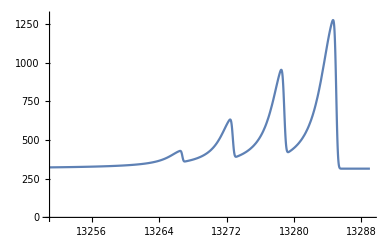
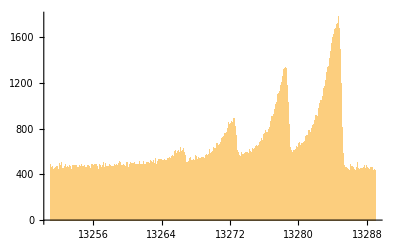

```mathematica
res=0.001;
freqs=Table[k,{k,13251,13289,res}];
m242Weights=Table[trooF[parms242,k],{k,13251,13289,res}];
totSamp242=RandomChoice[m242Weights->freqs,massCounts[242]];
{Plot[trooF[parms242,x],{x,13251,13289},PlotRange->{{13251,13289},{0,1300}}],
Histogram[totSamp242,{.01}]}
```

```mathematica
peakRanges={13262,13268,13274,13281,13289};
{m242counts3,m242counts2,m242counts1,m242counts0}=HistogramList[totSamp242,{peakRanges}][[2]]
```

{301571,367425,535613,636775}

```mathematica
freqs0=Table[k,{k,peakRanges[[4]],peakRanges[[5]],res}];m242Weights0=Table[trooF[parms242,k],{k,peakRanges[[4]],peakRanges[[5]],res}];
freqs1=Table[k,{k,peakRanges[[3]],peakRanges[[4]],res}];m242Weights1=Table[trooF[parms242,k],{k,peakRanges[[3]],peakRanges[[4]],res}];
freqs2=Table[k,{k,peakRanges[[2]],peakRanges[[3]],res}];m242Weights2=Table[trooF[parms242,k],{k,peakRanges[[2]],peakRanges[[3]],res}];
freqs3=Table[k,{k,peakRanges[[1]],peakRanges[[2]],res}];m242Weights3=Table[trooF[parms242,k],{k,peakRanges[[1]],peakRanges[[2]],res}];
Timing[m242μ0PolyEsts=SubSampleDistMaker4[m242Weights0,freqs0,m242counts0,{peakRanges[[4]],peakRanges[[5]],.01},{0},16,{13283.5,13285.5},1000];]
Timing[m242μ1PolyEsts=SubSampleDistMaker4[m242Weights1,freqs1,m242counts1,{peakRanges[[3]],peakRanges[[4]],.01},{0},16,{13277.5,13279.5},1000];]
Timing[m242μ2PolyEsts=SubSampleDistMaker4[m242Weights2,freqs2,m242counts2,{peakRanges[[2]],peakRanges[[3]],.01},{0},16,{13271.5,13273.5},1000];]
Timing[m242μ3PolyEsts=SubSampleDistMaker4[m242Weights3,freqs3,m242counts3,{peakRanges[[1]],peakRanges[[2]],.01},{0},16,{13265.5,13267.5},1000];]
```

{225.891,Null}

{210.063,Null}

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{192.438,Null}

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{198.609,Null}

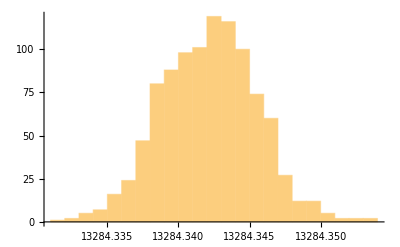

0.00336067

```mathematica
m242ℋPoly0=HistogramDistribution[m242μ0PolyEsts,{.001}];
Histogram[m242μ0PolyEsts,{.001}]
m242σPoly0=√Cumulant[m242ℋPoly0,2]
```

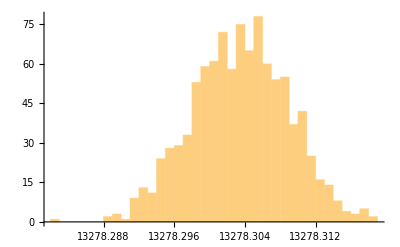

0.0054343

```mathematica
m242ℋPoly1=HistogramDistribution[m242μ1PolyEsts,{.001}];
Histogram[m242μ1PolyEsts,{.001}]
m242σPoly1=√Cumulant[m242ℋPoly1,2]
```

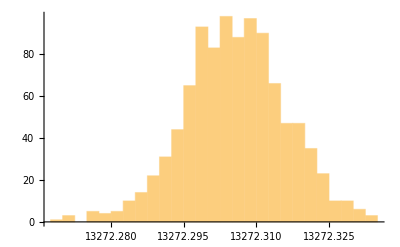

0.0104958

```mathematica
m242ℋPoly2=HistogramDistribution[m242μ2PolyEsts,{.0025}];
Histogram[m242μ2PolyEsts,{.0025}]
m242σPoly2=√Cumulant[m242ℋPoly2,2]
```

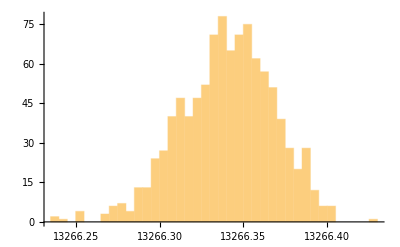

0.0280124

```mathematica
m242ℋPoly3=HistogramDistribution[m242μ3PolyEsts,{.005}];
Histogram[m242μ3PolyEsts,{.005}]
m242σPoly3=√Cumulant[m242ℋPoly3,2]
```

```mathematica
freqs0=Table[k,{k,peakRanges[[4]],peakRanges[[5]],res}];m242Weights0=Table[trooF[parms242,k],{k,peakRanges[[4]],peakRanges[[5]],res}];
freqs1=Table[k,{k,peakRanges[[3]],peakRanges[[4]],res}];m242Weights1=Table[trooF[parms242,k],{k,peakRanges[[3]],peakRanges[[4]],res}];
freqs2=Table[k,{k,peakRanges[[2]],peakRanges[[3]],res}];m242Weights2=Table[trooF[parms242,k],{k,peakRanges[[2]],peakRanges[[3]],res}];
freqs3=Table[k,{k,peakRanges[[1]],peakRanges[[2]],res}];m242Weights3=Table[trooF[parms242,k],{k,peakRanges[[1]],peakRanges[[2]],res}];
Timing[m242μ0PolyEsts=SubSampleDistMaker4[m242Weights0,freqs0,m242counts0,{peakRanges[[4]],peakRanges[[5]],.01},{0},16,{13283.5,13285.5},1000];]
Timing[m242μ1PolyEsts=SubSampleDistMaker4[m242Weights1,freqs1,m242counts1,{peakRanges[[3]],peakRanges[[4]],.01},{0},16,{13277.5,13279.5},1000];]
Timing[m242μ2PolyEsts=SubSampleDistMaker4[m242Weights2,freqs2,m242counts2,{peakRanges[[2]],peakRanges[[3]],.01},{0},16,{13271.5,13273.5},1000];]
Timing[m242μ3PolyEsts=SubSampleDistMaker4[m242Weights3,freqs3,m242counts3,{peakRanges[[1]],peakRanges[[2]],.01},{0},16,{13265.5,13267.5},1000];]
```

```mathematica
peakRanges={13262,13268,13274,13281,13289};guessRanges={{13265.5,13267.5},{13271.5,13273.5},{13277.5,13279.5},{13283.5,13285.5}};
```

```mathematica
isotopePolySigmaCalculator[m_,parms_,{kRange1_,kRange2_,res_},peakRanges_,bin_,guessRanges_,p_,nSamps_]:=(
freqs=Table[k,{k,kRange1,kRange2,res}];
mWeights=Table[trooF[parms,k],{k,kRange1,kRange2,res}];
mTotSamp=RandomChoice[mWeights->freqs,massCounts[m]];
countsList={counts3,counts2,counts1,counts0}=HistogramList[mTotSamp,{peakRanges}][[2]];
Table[(
freqsi=Table[k,{k,peakRanges[[i]],peakRanges[[i+1]],res}];
mWeights=Table[trooF[parms,k],{k,peakRanges[[i]],peakRanges[[i+1]],res}];
mPolyEsts=SubSampleDistMaker4[mWeights,freqsi,countsList[[i]],{peakRanges[[i]],peakRanges[[i+1]],bin},{0},p,guessRanges[[i]],nSamps];
ℋi=HistogramDistribution[mPolyEsts];σi=√Cumulant[ℋi,2];
{σi,mPolyEsts,"(this is for peak "<>ToString[4-i]<>")"}
),{i,Length[peakRanges]-1,1,-1}])
```

```mathematica
isotopePolySigmaCalculator[243,parms243,{13251,13289,.001},peakRanges,.01,guessRanges,16,10]
```

{{0.00702377,{13284.3,13284.3,13284.3,13284.2,13284.3,13284.2,13284.2,13284.3,13284.2,13284.3},(this is for peak 0)},{0.019218,{13278.2,13278.2,13278.1,13278.1,13278.2,13278.1,13278.2,13278.2,13278.2,13278.2},(this is for peak 1)},{0.0351188,{13272.2,13272.2,13272.2,13272.1,13272.1,13272.2,13272.1,13272.1,13272.1,13272.1},(this is for peak 2)},{0.0832666,{13266.1,13266.1,13266.2,13265.9,13266.,13266.1,13266.,13266.,13266.1,13266.1},(this is for peak 3)}}

```mathematica
Timing[m242Data=isotopePolySigmaCalculator[242,parms242,{13251,13289,.001},peakRanges,.01,guessRanges,16,1000];]
```

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{827.484,Null}

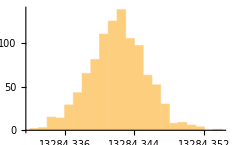
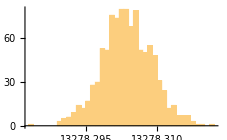
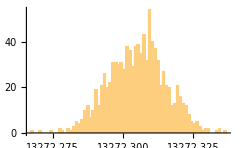
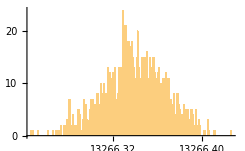

{{0.00325927,(this is for peak 0)},{0.00527841,(this is for peak 1)},{0.0103151,(this is for peak 2)},{0.0279123,(this is for peak 3)}}

```mathematica
Table[Histogram[m242Data[[i,2]],{.001}],{i,1,4}]
m242Uncerts=m242Data[[All,{1,3}]]
```

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NMaximize::cvmit will be suppressed during this calculation.

{650.469,Null}

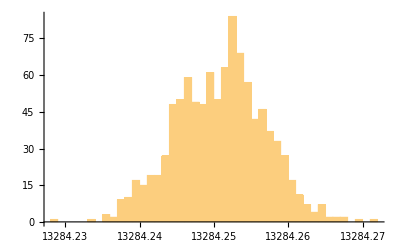
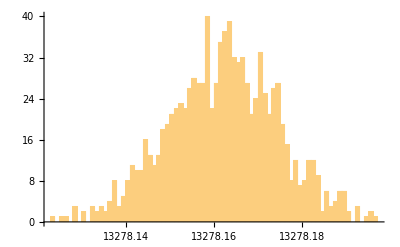
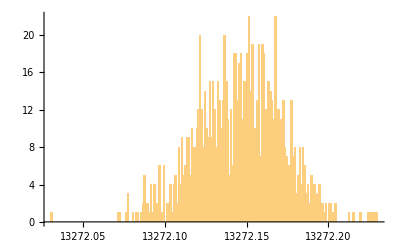
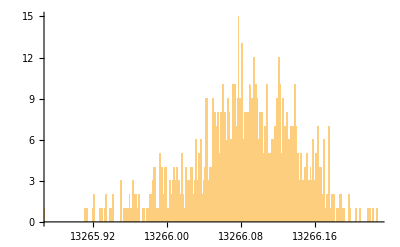

{{0.00607227,(this is for peak 0)},{0.0125778,(this is for peak 1)},{0.0263143,(this is for peak 2)},{0.0627607,(this is for peak 3)}}

```mathematica
Timing[m243Data=isotopePolySigmaCalculator[243,parms243,{13251,13289,.001},peakRanges,.01,guessRanges,16,1000];]
Table[Histogram[m243Data[[i,2]],{.001}],{i,1,4}]
m243Uncerts=m243Data[[All,{1,3}]]
```

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{646.75,Null}

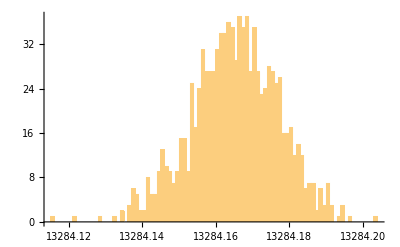
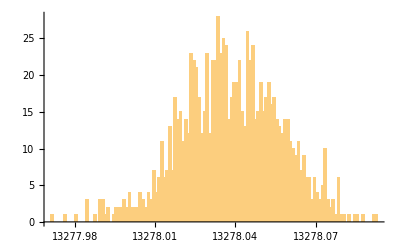
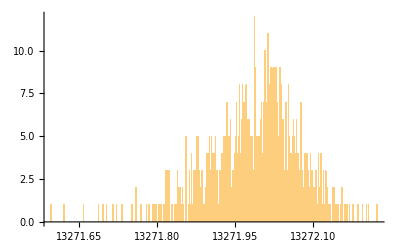
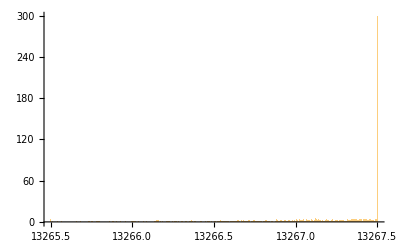

{{0.0119918,(this is for peak 0)},{0.0189254,(this is for peak 1)},{0.0828544,(this is for peak 2)},{0.401411,(this is for peak 3)}}

```mathematica
Timing[m244Data=isotopePolySigmaCalculator[244,parms244,{13251,13289,.001},peakRanges,.01,guessRanges,16,1000];]
Table[Histogram[m244Data[[i,2]],{.001}],{i,1,4}]
m244Uncerts=m244Data[[All,{1,3}]]
```

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NMaximize::cvmit will be suppressed during this calculation.

{800.,Null}

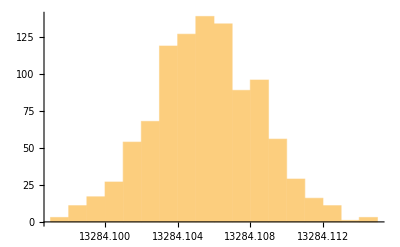
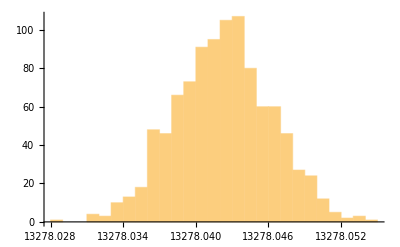
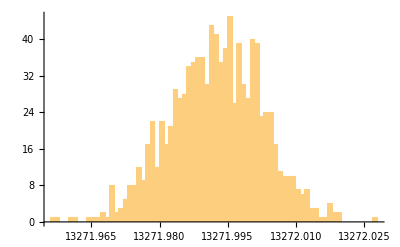
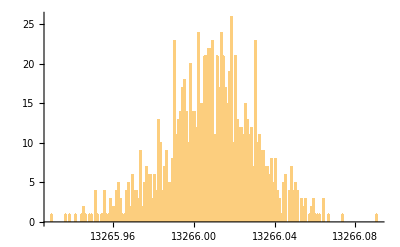

{{0.00292821,(this is for peak 0)},{0.00396081,(this is for peak 1)},{0.0103864,(this is for peak 2)},{0.0232137,(this is for peak 3)}}

```mathematica
Timing[m245Data=isotopePolySigmaCalculator[245,parms245,{13251,13289,.001},peakRanges,.01,guessRanges,16,1000];]
Table[Histogram[m245Data[[i,2]],{.001}],{i,1,4}]
m245Uncerts=m245Data[[All,{1,3}]]
```

{699.672,Null}

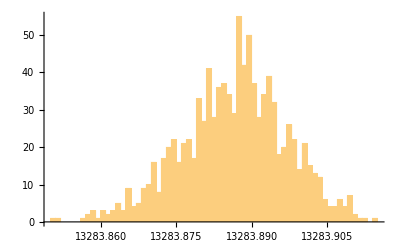
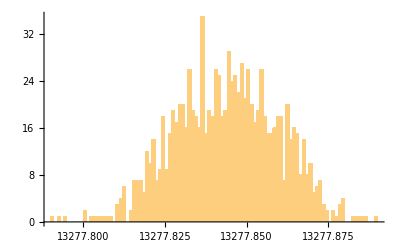
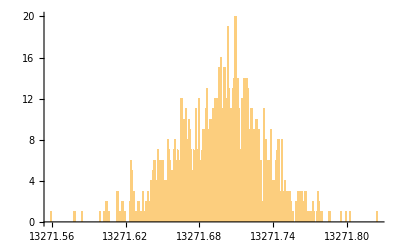
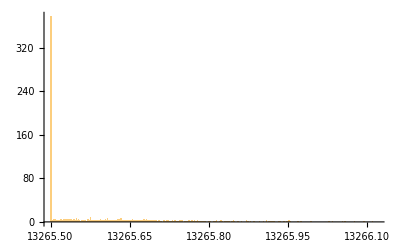

{{0.010518,(this is for peak 0)},{0.0158774,(this is for peak 1)},{0.0352553,(this is for peak 2)},{0.509532,(this is for peak 3)}}

```mathematica
Timing[m247Data=isotopePolySigmaCalculator[247,parms247,{13251,13289,.001},peakRanges,.01,guessRanges,16,1000];]
Table[Histogram[m247Data[[i,2]],{.001}],{i,1,4}]
m247Uncerts=m247Data[[All,{1,3}]]
```

```mathematica
"polyMaxStdErr[242] = "<>ToString[m242Data[[All,1]]]
"polyMaxStdErr[243] = "<>ToString[m243Data[[All,1]]]
"polyMaxStdErr[244] = "<>ToString[m244Data[[All,1]]]
"polyMaxStdErr[245] = "<>ToString[m245Data[[All,1]]]
"polyMaxStdErr[247] = "<>ToString[m247Data[[All,1]]]
```

polyMaxStdErr[242] = {0.00325927, 0.00527841, 0.0103151, 0.0279123}
polyMaxStdErr[243] = {0.00607227, 0.0125778, 0.0263143, 0.0627607}
polyMaxStdErr[244] = {0.0119918, 0.0189254, 0.0828544, 0.401411}
polyMaxStdErr[245] = {0.00292821, 0.00396081, 0.0103864, 0.0232137}
polyMaxStdErr[247] = {0.010518, 0.0158774, 0.0352553, 0.509532}